```mathematica
x = ;
```

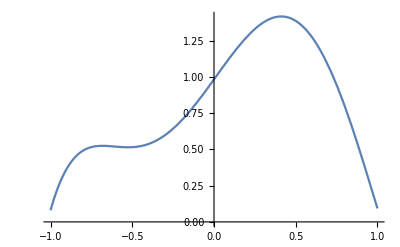

```mathematica
f[t_] = 0.4(0.2+25(0.4t+0.4)-200(0.4t+0.4)^2+675(0.4t+0.4)^3 - 900(0.4t+0.4)^4+400(0.4t+0.4)^5);
Plot[f[t], {t,-1,1}]
```

```mathematica
gaussIntegral2 = f[-1/Sqrt[3]]+f[1/Sqrt[3]]
```

1.82258

```mathematica
gaussIntegram3 = 5/9*f[-√(3/5)]+8/9 f[0]+5/9(f[√(3/5)])
```

1.64053

```mathematica
trapezoid = Abs[f[-1]+f[1]]
```

0.1728

```mathematica
rectangle = 2*f[0]
```

1.9648

```mathematica
simpson = Abs[1/3*(f[1]+4*f[0]+f[1])]
```

1.37173

```mathematica
Integrate[f[t], {t,-1,1}]
```

1.64053

```mathematica
Solve[{Integrate[1*(x^2+b*x+c), {x,0,1}]==0, Integrate[(x+2/3)*(x^2+b*x+c),{x,0,1}]==0} {b,c}]
```

Integrate::ilim: Invalid integration variable or limit(s) in {0.4+0.4 t,0,1}.

Solve::naqs: b (∫_0^1 (c+b (0.4+Times[«2»])+(0.4+Times[«2»])^2)ⅆ(0.4+0.4 t)==0)&&c (∫_0^1 (c+b Plus[«2»]+Plus[«2»]^2) (1.06667+0.4 t)ⅆ(0.4+0.4 t)==0) is not a quantified system of equations and inequalities.

Solve[{b (∫_0^1 (c+b (0.4+0.4 t)+(0.4+0.4 t)^2)ⅆ(0.4+0.4 t)==0),c (∫_0^1 (c+b (0.4+0.4 t)+(0.4+0.4 t)^2) (1.06667+0.4 t)ⅆ(0.4+0.4 t)==0)}]